```mathematica
ClearAll["`*"];
(*Tmax=0.3/J*40;*)
Tmax=40;
Tnum=1000;

NN=12; (* site number *)
outfile=StringJoin["N",ToString[NN],".wdx"];


SetDirectory[NotebookDirectory[]]
Trans=Transpose;
Htran=ConjugateTranspose;
Kron=KroneckerProduct;
Conj=Conjugate;
EntroS[P_]:=Sum[
If[0<P⟦n⟧<1,-P⟦n⟧Log[P⟦n⟧],0],{n,1,Length[P]}];
VOV[v1_,Opt_,v2_]:=(Htran[v1].Opt.v2)⟦1,1⟧;
VOV[v1_,Opt_]:=(Htran[v1].Opt.v1)⟦1,1⟧; (* v1, v2 should be right ket *)
VV[v1_,v2_]:=(Htran[v1].v2)⟦1,1⟧;
Zeros[MM_,NN_]:=SparseArray[{1,1}->0,{MM,NN}];
Ident[n_]:=IdentityMatrix[n] 
Dij[a_,b_]:=If[a==b,1,0] (* delta_ij *)
```

/Users/steven/Nextcloud/NetDisk/Works/NonBoltz/Code/scale

```mathematica
(*== Generate Index mappings, operator functions ==*)


DNN=3^NN; (* Total dimension *)
DD=NN(NN-1)(NN+4)/6; (* subspace dimention*)

Print["Site number: ",NN]
Print["subspace dimension: ",DD]

C3=Subsets[Range[NN],{3}]; (* { {1,2,3},{1,2,4},... } *)
C2a=C2b=Subsets[Range[NN],{2}]; (* { {1,2},{1,3},... } *)
Do[{x,y}=C2a⟦n⟧;
C2a⟦n⟧={x,x,y};C2b⟦n⟧={x,y,y},
{n,1,Length[C2a]}]; 
(* C2a={ {1,1,2},{1,1,3},... }, C2b={ {1,2,2},{1,3,3},... } *)
DC3=Length[C3];
DC2=Length[C2a];
Cs=Join[C3,C2a,C2b]; (* All indices combinations {C3, C2a, C2b} *)

(*-- Generate |a,b,c>  --*)
Vidx[a_,b_,c_]:=Module[{x},
x=Position[Cs,Sort[{a,b,c}]]⟦1,1⟧;
SparseArray[{x,1}->1,{DD,1}]
]
Vidx[as_]:=Module[{x},
x=Position[Cs,Sort[as]]⟦1,1⟧;
SparseArray[{x,1}->1,{DD,1}]
]

  (*-- Subscript[S, n]^+Subscript[S, n+d]^- --*)
OpSnpSndm[n_,d_:1]:=Module[{SSn,nx,r1s,r2s,b,r,x,y},
SSn=Zeros[DD,DD];
nx=n+d;
If[nx>NN,nx=nx-NN]; (* n+d *)
r1s=Delete[Range[NN],n];
r1s=Delete[r1s,Position[r1s,nx]⟦1,1⟧];
r1s=Trans[{r1s,r1s}];
r2s=Subsets[Range[NN],{2}];(* Subsets[] along cannot generate elments like {x,x} *)
r2s=Join[r1s,r2s]; 
 (*-- All combination of b,r (cannot equal to n+d,n together) --*)
(*---  <n,b,r|Subscript[S, n]^+Subscript[S, n+1]^-|n+1,b,r> = <x|O|y> ---*)
Do[{b,r}=br;
x=Position[Cs,Sort[{n,b,r}]]⟦1,1⟧;
y=Position[Cs,Sort[{nx,b,r}]]⟦1,1⟧;
(*Print[n,b,r,":",x," ",y];*)
SSn⟦x,y⟧=2,
{br,r2s}];
SSn]

  (*-- Subscript[P, n,a] a={0,1,2} -> {-1,0,+1} --*)
OpNna[n_,a_]:=Module[{Nna,rs,brs,x},
Nna=Ident[DD]*Dij[a,0];
(*---  <n,n,r|Nna|n,n,r>,  <n,r,r|Nna|n,r,r>  ---*)
rs=Delete[Range[NN],n];
Do[
x=Position[Cs,Sort[{n,n,r}]]⟦1,1⟧;
Nna⟦x,x⟧=Dij[a,2];
x=Position[Cs,Sort[{n,r,r}]]⟦1,1⟧;
Nna⟦x,x⟧=Dij[a,1],
{r,rs}];
(*---  <n,b,r|Nna|n,b,r>  ---*)
brs=Subsets[rs,{2}];
Do[x=Position[Cs,Sort[Flatten[{br,n}]]]⟦1,1⟧;
Nna⟦x,x⟧=Dij[a,1],
{br,brs}];
Nna]

 (*-- Subscript[S, n]^z, Subscript[D, n]^z --*)
OpSnz[n_]:=-OpNna[n,0]+OpNna[n,2]
OpDnz[n_]:=OpNna[n,0]+OpNna[n,2]
```

Site number: 12

subspace dimension: 352

```mathematica
(*== Generate Tables for operators ==*)

(*-- List of All Subscript[N, n,a] --*)
OpNnas=ParallelTable[OpNna[n,a],{n,1,NN},{a,0,2}];  
OpSnzs=-OpNnas⟦;;,1⟧+OpNnas⟦;;,3⟧;
OpDnzs=OpNnas⟦;;,1⟧+OpNnas⟦;;,3⟧;
OpNas=ParallelTable[1./NN Sum[OpNna[n,a],{n,1,NN}],{a,0,2}];
```

```mathematica
(*-- Initial state --*)
idx=Sort[{1,2,3}];
V0=Vidx[idx];

J=0.3;Ω=-1;ω=-0.13;
E0=0.; Ep1=Ω+ω; Em1=Ω-ω;

Print["E_-1=",Em1,"  E_0=",E0,"  E_(+1)=",Ep1]
Print["Interaction J=",J]
H0=ParallelSum[Em1*OpNnas⟦n,1⟧+E0*OpNnas⟦n,2⟧+Ep1*OpNnas⟦n,3⟧,{n,1,NN}];
Hv=ParallelSum[J*OpSnpSndm[n],{n,1,NN}];
Hv=Hv+Htran[Hv];
HH=Hv+H0;

{vals,vecs}=Eigensystem[HH];
Print["HH Eigen solved. ",DateString["Time"]]
```

E_-1=-0.87  E_0=0.  E_(+1)=-1.13

Interaction J=0.3

HH Eigen solved. 20:34:35

```mathematica
Print["Tmax: ",Tmax];
Print["Size N: ",NN];
V01=vecs.V0; 
Vt=ParallelTable[Htran[vecs].DiagonalMatrix[Exp[-I t vals]].V01,{t,0,Tmax,Tmax/Tnum}];
Print["Vt: ",DateString["Time"]]

Pnat=ParallelTable[Re[VOV[Vt⟦t⟧,OpNnas⟦n,a⟧]],
{n,1,NN},{a,1,3},{t,1,Length[Vt]}]; 

Export[outfile,Pnat]
```

Tmax: 40

Size N: 12

Vt: 20:34:38

N12.wdx

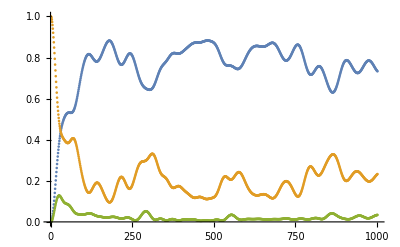

```mathematica
n=1;
ListPlot[{Pnat⟦n,1,;;⟧,Pnat⟦n,2,;;⟧,Pnat⟦n,3,;;⟧},PlotRange->All]
```